```mathematica
h=0.0037
Y=397.903 10^9
R=0.015
σ=0.29
```

0.0037

3.97903×10^11

0.015

0.29

```mathematica
Dc=(Y h^3)/(12(1-σ^2))
```

1833.8

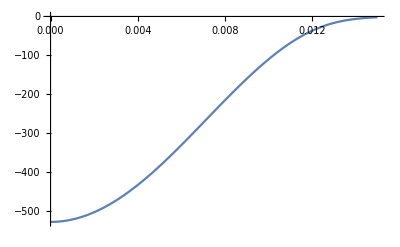

```mathematica
Plot[Mf[x],{x,0,R}]
```

```mathematica
Mf2=Interpolation[Table[{x,Integrate[y Mf[y],{y,0,Abs[x]}]},{x,-R,R,0.001}],InterpolationOrder->4];
```

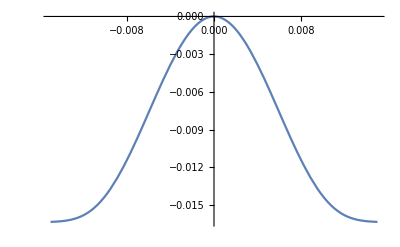

```mathematica
Plot[Mf2[x],{x,-R,R}]
```

```mathematica
Mf3=Interpolation[Table[{x,Integrate[1/y Mf2[y],{y,0,x}]},{x,-R,R,0.001}]]
```

InterpolatingFunction[{{-0.015, 0.015}}, <>]

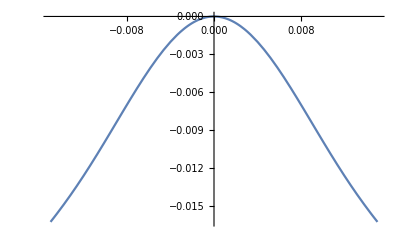

```mathematica
Plot[Mf3[x],{x,-R,R}]
```

```mathematica
κϕ[r_]:=1/r^2 Mf2[r]
```

```mathematica
κr[r_]:=(D[1/r1 Mf2[r1],r1])/.r1->r
```

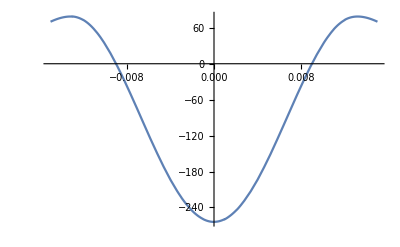

```mathematica
Plot[κr[x],{x,-R,R}]
```

```mathematica
ξo[r_]:=c1 r^2
```

```mathematica
κr1[r_]:=2 c1
```

```mathematica
κϕ1[r_]:=2 c1
```

```mathematica
s=Solve[κr[R]+σ κϕ[R]+κr1[R]+σ κϕ1[R]==0,c1];
```

```mathematica
ξ[r_]:=1/Dc(Mf3[r]-ξo[r])/.s[[1]]
```

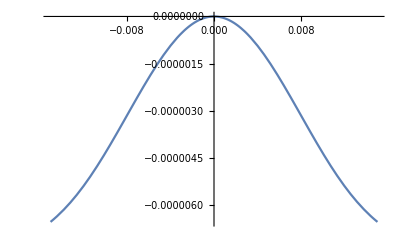

```mathematica
Plot[ξ[r],{r,-R,R}]
```

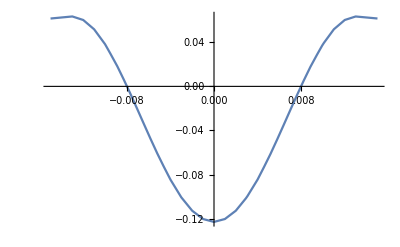

```mathematica
Plot[(D[ξ[r],{r,2}])/.r->r1,{r1,-R,R}]
```